```mathematica
coeffRabbitRate=RandomReal[{0,1}];coeffRabbitReductionByCrow=RandomReal[{-0.1,0}];
coeffCrowReductionRate=RandomReal[{-1,0}];
coeffRabbitConsumptionByCrow=RandomReal[{0,0.1}];
coeffWeatherAdjustment=RandomReal[{0,1}];
weatherAccountability[t]=-Cos[0.5t]^2;
```

```mathematica
rabbitRateEqn=r'[t]==r[t](coeffRabbitRate+coeffRabbitReductionByCrow*k[t]+coeffWeatherAdjustment*weatherAccountability[t])
```

r'[t]==(0.804143-0.428901 Cos[0.5 t]^2-0.0541726 k[t]) r[t]

```mathematica
crowRateEqn=k'[t]==k[t](coeffCrowReductionRate+coeffRabbitConsumptionByCrow*r[t]+coeffWeatherAdjustment*weatherAccountability[t])
```

k'[t]==k[t] (-0.884659-0.428901 Cos[0.5 t]^2+0.0963988 r[t])

```mathematica
solRabbitCrow=NDSolve[
{rabbitRateEqn,crowRateEqn,r'[0]==8,k'[0]==2},
{r,k},{t,0,400}]
```

{{r→InterpolatingFunction[…],k→InterpolatingFunction[…]}}

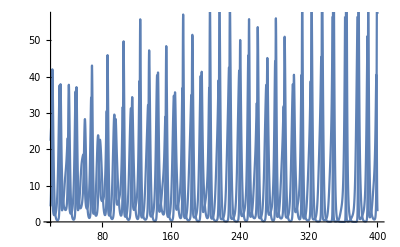

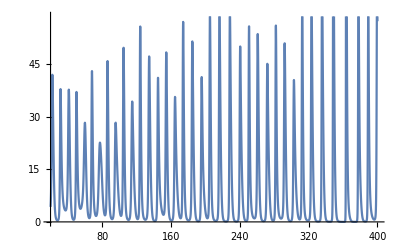

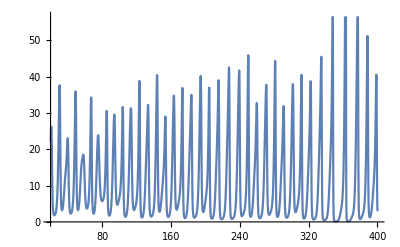

```mathematica
rabbitPlot=Plot[r[t]/.solRabbitCrow,{t,20,400}];
crowPlot=Plot[k[t]/.solRabbitCrow,{t,20,400}];
Show[{rabbitPlot,crowPlot}]
crowPlot
rabbitPlot
```